# Mean-Median Map Project

In this project we will investigate the Mean-Median Map. The claims that we will try to prove in this project come from a this paper 
Hyperlink[“http://www.math.grin.edu/~chamberl/papers/mean_median.pdf”]. 

The Mean-Median Map deals with finding the next number in a sequence which makes the mean equal to the median.  There comes a point in this sequence where the number that is added is the same as the previous number and continues to be so indefinitely. Now we will start by proving the claims.

## Preliminary Function:

Before we start proving the theorems required by the project we should first have a function that defines the next value.

```mathematica
nextVal[vals_]:=Module[{med,ret,n},
med=Median[vals];(*Find the median*)
n=Length[vals]+1;(*Length of the list + 1 for the added new value*)
ret=Simplify[n*med-Total[vals]];(*the new value that makes the mean equal to the median*)
ret
]
```

This function finds the next value that makes the mean of the sequence of numbers equal to the median. This function will be used throughout the project.

## Theorem 2.1

Theorem 2.1 states that the sequence of medians is monotone. This means that the list of means generated by adding new numbers will either be increasing or decreasing. We will write a function that generates a list of medians and then we will check if this list is monotone

The following function will calculate the medians every time a new number is added to the list and will save those in a list which whill be returned in the end

```mathematica
medianGenerator[initSeq0_]:=Module[{
currSeq=initSeq0,
sortSeq,totVal,medVal,lastVal,currVal,n},
(* initial total and sorted sequence*)
totVal=Total[initSeq0];(*calculate the total value*)
sortSeq=Sort[initSeq0];(*sort the sequence*)
(* these are needed at each step *)
n=Length[initSeq0];
lastVal=initSeq0[[-2]];(*define last value*)
currVal=initSeq0[[-1]];(*define current value*)
med = Median[currSeq];(*find the median*)
(*create a list with medians, put the first median in, this will be very important since we will return this list *)
medians ={med};
While[lastVal≠currVal ,
(* Median is easy to find on a sorted list *)
medVal=If[OddQ[n],
sortSeq[[(n+1)/2]],
1/2*(sortSeq[[n/2]]+sortSeq[[n/2+1]])];
(* redo last and current values using the pre-computed 
median and total*)
lastVal=currVal;(*save the curr value as the last one*)
currVal=(n+1)*medVal-totVal;(*find the currVal using the formula*)
(* append to our current sequence and increment n *)
AppendTo[currSeq,currVal];
med = Median[currSeq];(*find the new median*)
(*append the new median to the medians list*)
AppendTo[medians,med];
(* Increment the total *)
n++;
totVal=totVal+currVal;
(* Resort. Sorting an almost sorted list is pretty fast *)
sortSeq=Sort[AppendTo[sortSeq,currVal]];
];
Delete[currSeq,-1];
Return[medians]; (*return the list of medians that we will plot*)
]
```

Now let’s try if our function works with an example list.

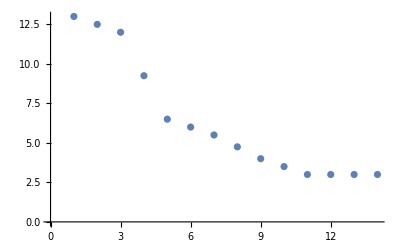

```mathematica
vals0={1,3,17,13,14,12,3,4,134,1234234,23}; (*define a list*)
l1 = medianGenerator[vals0]; (*call the function that generates medians*)
ListPlot[l1]
```

As we see from this example our function works! Now we have to try it in a large scale. 

To prove this I will generate 10 random numbers n. I will create 10 lists with n random numbers and I will see if the mean is monotone for each of those lists.

```mathematica
listOfPlots ={}; (*list that will hold all our lists of medians*)
For[i=0,i<10,i++,
randomLength = RandomInteger[{10,100}]; (*generate random length*)
randomList ={};(*define an empty random list*)
For[x=0,x<randomLength,x++,
rInt = RandomInteger[{-10000,10000}]; (*chose a random int*)
AppendTo[randomList,rInt]; (*append it to the random list*)
];
(*get the list of medians for one sequence*)
l2 = medianGenerator[randomList];
(*append this list to the list that will hold all lists of medians*)
AppendTo[listOfPlots, l2];
]
```

Let’s check that our list of plots actually works and let’s try to plot each list:

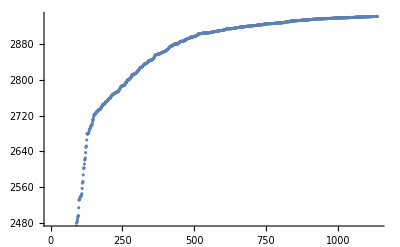

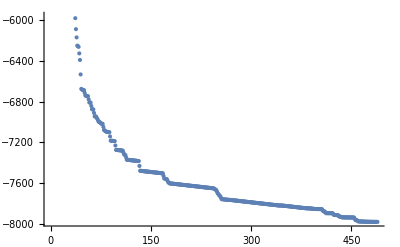

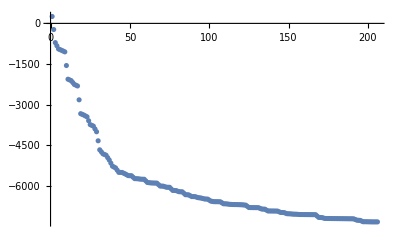

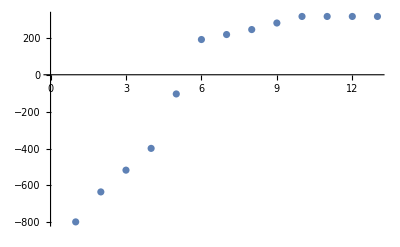

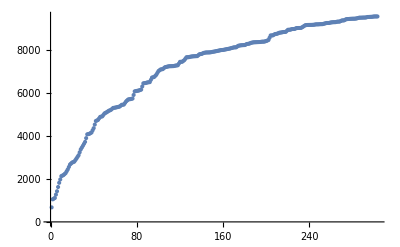

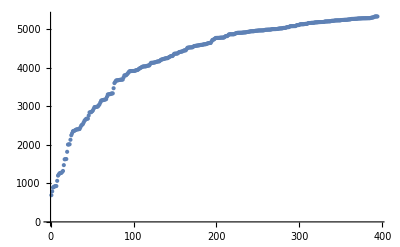

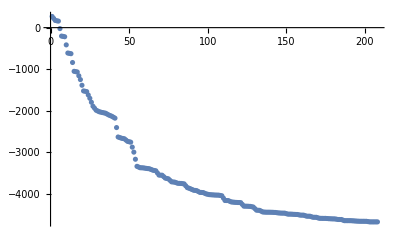

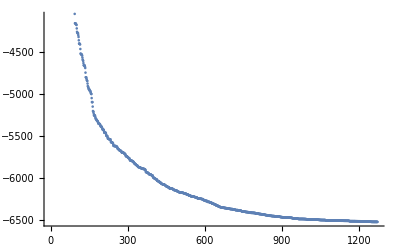

```mathematica
ListPlot[listOfPlots[[1]]] 
ListPlot[listOfPlots[[2]]] 
ListPlot[listOfPlots[[3]]] 
ListPlot[listOfPlots[[4]]] 
ListPlot[listOfPlots[[5]]] 
ListPlot[listOfPlots[[6]]] 
ListPlot[listOfPlots[[7]]] 
ListPlot[listOfPlots[[8]]] 
ListPlot[listOfPlots[[9]]] 
ListPlot[listOfPlots[[10]]]
```

As we see from all the graphs the medians are either increasing or decreasing. Even though we only looked at 10 examples those examples were of random lengths and random integers inside those lengths.

## Proof of the Strong Terminating Conjecture

The strong terminating conjecture states that the sequence of new terms settles permanently to the median after a finite number of mean-median iterations. To prove this I will just add another checker to the medianGenerator function that we wrote above. The while loop now will make sure that the current value also equals the median before we stop the loop. If the loop stops it means that  the sequence of new terms settles permanently to the median after a finite number of mean-median iterations.

```mathematica
medianChecker[initSeq0_]:=Module[{
currSeq=initSeq0,
sortSeq,totVal,medVal,lastVal,currVal,n},
(* initial total and sorted sequence*)
totVal=Total[initSeq0];(*calculate the total value*)
sortSeq=Sort[initSeq0];(*sort the sequence*)
(* these are needed at each step *)
n=Length[initSeq0];
lastVal=initSeq0[[-2]];(*define last value*)
currVal=initSeq0[[-1]];(*define current value*)
med = Median[currSeq];(*find the median*)
While[lastVal≠currVal && med≠currVal,
(* Median is easy to find on a sorted list *)
medVal=If[OddQ[n],
sortSeq[[(n+1)/2]],
1/2*(sortSeq[[n/2]]+sortSeq[[n/2+1]])];
(* redo last and current values using the pre-computed 
median and total*)
lastVal=currVal;(*save the curr value as the last one*)
currVal=(n+1)*medVal-totVal;(*find the currVal using the formula*)
(* append to our current sequence and increment n *)
AppendTo[currSeq,currVal];
med = Median[currSeq];(*find the new median*)
(* Increment the total *)
n++;
totVal=totVal+currVal;
(* Resort. Sorting an almost sorted list is pretty fast *)
sortSeq=Sort[AppendTo[sortSeq,currVal]];
];
Delete[currSeq,-1];
Return[1];(*just to check that it finished*)
]
```

Again let’s try if this loop stops for our example same as in the first part.

```mathematica
medianChecker[vals0]
```

1

Since we don’t have an infinite loop and the function finishes let’s try do the same thing but now with 100 random lists of random lengths and random lengths and random integers and see if those finish and we don’t run in an infinite loop. If so then we have proven the Strong Terminating Conjecture.

```mathematica
For[i=0,i<100,i++,
randomLength = RandomInteger[{10,1000}]; (*generate random length*)
randomList ={};(*define an empty random list*)
For[x=0,x<randomLength,x++,
rInt = RandomInteger[{-10000,10000}]; (*chose a random int*)
AppendTo[randomList,rInt]; (*append it to the random list*)
];
(*get the list of medians for one sequence*)
l2 = medianChecker[randomList];
]
Print[l2]
```

1

As we see it takes a few seconds but it runs for 100 lists of random elements and lengths and thus proving the Strong Terminating Conjecture.

## Proving that the function is unbounded

In this part of the lab we shall prove that the number of steps required for the sequence to settle is not bounded. The way I will chose to do this is to show that as we increase the range of random numbers to chose from we will need more steps. 

First thing we need is to define a function that counts the steps.

```mathematica
numSteps[initSeq_]:=Module[
{numSteps=0,
(* Initialize these values *)
lastVal=initSeq[[-2]],
currVal=initSeq[[-1]],
currSeq=initSeq},
While[lastVal ≠  currVal,
(* promote lastVal and compute nextVal *)
lastVal=currVal;
currVal=nextVal[currSeq];
(*Append currVal to the currSeq*)
AppendTo[currSeq,currVal];
numSteps++
];
Return[numSteps]; 
]
```

Now just as before let’s use our double loop to create a list of random lists with random lengths. Then we will print the number of steps.

```mathematica
For[i=0,i<10,i++,
randomLength = RandomInteger[{10,100}]; (*generate random length*)
randomList ={};(*define an empty random list*)
For[x=0,x<randomLength,x++,
rInt = RandomInteger[{-1000,1000}]; (*chose a random int*)
AppendTo[randomList,rInt]; (*append it to the random list*)
];
(*get the list of medians for one sequence*)
steps = numSteps[randomList];
Print[steps]
]
```

340

30

28

94

43

8

133

59

16

864

Now let’s see how the number of steps changes as we increase the range of random numbers we choose from to put in our random list.

```mathematica
For[i=0,i<10,i++,
randomLength = RandomInteger[{10,100}]; (*generate random length*)
randomList ={};(*define an empty random list*)
For[x=0,x<randomLength,x++,
(*change the length by a factor of ten*)
rInt = RandomInteger[{-10000,10000}]; 
AppendTo[randomList,rInt]; (*append it to the random list*)
];
(*get the list of medians for one sequence*)
steps = numSteps[randomList];
Print[steps]
]
```

264

326

86

2123

106

764

308

1292

319

116

As we see the numbers increased. This proves that the function is unbounded and the number of steps will increase. (Run this a few times for the numbers to be large). This happens since I am randomly choosing the numbers.

## My own conjectures

The first conjecture that we I will make is that the number of steps will increase as numbers are in a wider range. Proof for that can be seen in the part where I was proving that the function is unbounded. When I increased the range of random numbers from -1000 to 1000, to -10 000 to 10 000 the number of steps increased. 

The next claim that I will make is that when the length of list increases but the range where elements are picked, or another way to say this is that the variety of numbers is kept the same, then the number of steps will decrease. Let’s put this to try

First time we will keep the length still random from 10 to 100 and the range for the elements from -10000 to 10000 and we will count the number of steps.

```mathematica
For[i=0,i<10,i++,
randomLength = RandomInteger[{10,100}]; (*generate random length*)
randomList ={};(*define an empty random list*)
listSteps1 ={};
For[x=0,x<randomLength,x++,
(*change the length by a factor of ten*)
rInt = RandomInteger[{-10000,10000}]; 
AppendTo[randomList,rInt]; (*append it to the random list*)
];
(*get the list of medians for one sequence*)
steps = numSteps[randomList];
AppendTo[listSteps1,steps];
]
Mean[listSteps1](*find the mean of steps for all 10 lists*)
```

366

Now we will keep the range the same but the length will be anywhere from 10000 to 20000 and let’s see what the number of steps will be:

```mathematica
For[i=0,i<10,i++,
randomLength = RandomInteger[{10000,20000}]; (*generate random length*)
randomList ={};(*define an empty random list*)
listSteps2 ={};
For[x=0,x<randomLength,x++,
(*change the length by a factor of ten*)
rInt = RandomInteger[{-10000,10000}]; 
AppendTo[randomList,rInt]; (*append it to the random list*)
];
(*get the list of medians for one sequence*)
steps = numSteps[randomList];
AppendTo[listSteps2, steps];
]
Mean[listSteps2](*find the mean of steps for all 10 lists*)
```

5

What is interesting here is that the number of steps decreases as the length of the list increases but the range we chose stays the same. This was different to what I had thought. 

So it seems that the variety of numbers in a list will increase the number of steps, and an increase in length of the list will decrease the number of steps!